```mathematica
(* Begin of the header of the computations and all functions  *)
```

```mathematica
ϕ[t_]:=Exp[-t];
weight[X_?VectorQ,constant_]:=ϕ[Norm[X]/(3constant)];
weightfunction[var_,constant_]:=ϕ[var/(3constant)];
```

```mathematica
NonEquLen::noneqlenght="The arguments have not equal lenghts.";
```

```mathematica
GenMean1D[setPoints_,testPoint_]:=Module[{setPointsZ=setPoints,testPointZ=testPoint,testPointZZ,vectorZZ,lenghtZ,distVectorZ,HZ,WFTZ},
If[VectorQ[setPointsZ]&&NumberQ[testPointZ],
lenghtZ=Length[setPointsZ];
distVectorZ=DistanceMatrix[setPointsZ,{testPointZ}];
HZ=Total[distVectorZ]/lenghtZ;
WFTZ=Table[weightfunction[Norm[setPointsZ[[i]]-testPointZ],HZ],{i,lenghtZ}];
First[Sum[setPointsZ[[i]]WFTZ[[i]],{i,lenghtZ}]/Total[WFTZ]],Message[NonEquLen::noneqlenght]]]
```

```mathematica
GenMean[setPoints_,testPoint_]:=Module[{setPointsZ=setPoints,testPointZ=testPoint,lenghtZ,lZZ1,lZZ2},
If[VectorQ[setPointsZ]&&NumberQ[testPointZ],GenMean1D[setPointsZ,testPointZ],
(lZZ1=Dimensions[setPointsZ][[2]];
lZZ2=Length[testPointZ];
If[lZZ1==lZZ2,
Table[GenMean1D[setPointsZ[[All,j]],testPointZ[[j]]],{j,lZZ1}]
,Message[NonEquLen::noneqlenght]])]]
```

```mathematica
GenCovVec1D[setPointsX_?VectorQ,setPointsY_?VectorQ,testPointX_,testPointY_]:=Module[{setPointsXZ=setPointsX,setPointsYZ=setPointsY,testPointXZ=testPointX,testPointYZ=testPointY,lZ1,lZ2,NewSetXZ,NewSetYZ,sumZ,distVectorXZ,distVectorYZ,HXZ,HYZ,WFTXZ,WFTYZ},
lZ1=Length[setPointsXZ];
lZ2=Length[setPointsYZ];
If[lZ1==lZ2,
distVectorXZ=DistanceMatrix[setPointsXZ,{testPointXZ}];
distVectorYZ=DistanceMatrix[setPointsYZ,{testPointYZ}];
HXZ=Total[distVectorXZ]/lZ1;
HYZ=Total[distVectorYZ]/lZ2;
WFTXZ=Flatten[Table[weightfunction[Norm[setPointsXZ[[i]]-testPointXZ],HXZ],{i,lZ1}]];
WFTYZ=Flatten[Table[weightfunction[Norm[setPointsYZ[[i]]-testPointYZ],HYZ],{i,lZ2}]];
NewSetXZ=(setPointsXZ-GenMean[setPointsXZ,testPointXZ])Sqrt[WFTXZ];
NewSetYZ=(setPointsYZ-GenMean[setPointsYZ,testPointYZ])Sqrt[WFTYZ];
sumZ=Total[Sqrt[WFTXZ]Sqrt[WFTYZ]];

(NewSetXZ.Conjugate[NewSetYZ])/(sumZ-1),Message[NonEquLen::noneqlenght]]]
```

```mathematica
GenCovVec[setPointsX_?VectorQ,setPointsY_?VectorQ,testPointX_,testPointY_]:=Module[{setPointsXZ=setPointsX,testPointXZ=testPointX,setPointsYZ=setPointsY,testPointYZ=testPointY},
GenCovVec1D[setPointsXZ,setPointsYZ,testPointXZ,testPointYZ]
]
```

```mathematica
GenCovVec[setPointsX_?VectorQ,testPointX_]:=Module[{setPointsXZ=setPointsX,testPointXZ=testPointX},
GenCovVec1D[setPointsXZ,setPointsXZ,testPointXZ,testPointXZ]
]
```

```mathematica
GenCovMatN[setPointsX_?MatrixQ,setPointsY_?MatrixQ,testPointX_,testPointY_]:=Module[{setPointsXZ=setPointsX,setPointsYZ=setPointsY,testPointXZ=testPointX,testPointYZ=testPointY,dimZ1,dimZ2,i,j,gencovmatZ,GenCovMatZ},
dimZ1=Dimensions[setPointsXZ];
dimZ2=Dimensions[setPointsYZ];
If[First[dimZ1]==First[dimZ2]&&Length[testPointXZ]==dimZ1[[2]]&&Length[testPointYZ]==dimZ2[[2]],
For[i=1,i≤dimZ1[[2]],i++,
For[j=1,j≤dimZ2[[2]],j++,
gencovmatZ[i,j]=GenCovVec[setPointsXZ[[All,i]],setPointsYZ[[All,j]],testPointXZ[[i]],testPointYZ[[j]]]]];
GenCovMatZ=Table[gencovmatZ[i,j],{i,dimZ1[[2]]},
{j,dimZ2[[2]]}]
,Message[NonEquLen::noneqlenght]]]
```

```mathematica
GenCovMat[setPointsX_?MatrixQ,setPointsY_?MatrixQ,testPointX_,testPointY_]:=Module[{setPointsXZ=setPointsX,setPointsYZ=setPointsY,testPointXZ=testPointX,testPointYZ=testPointY},
GenCovMatN[setPointsXZ,setPointsYZ,testPointXZ,testPointYZ]
]
```

```mathematica
GenCovMat[setPointsX_?MatrixQ,testPointX_]:=Module[{setPointsXZ=setPointsX,testPointXZ=testPointX},
GenCovMat[setPointsXZ,setPointsXZ,testPointXZ,testPointXZ]
]
```

```mathematica
GenCovariance[setPointsX_,setPointsY_,testPointX_,testPointY_]:=Module[{setPointsXZ=setPointsX,setPointsYZ=setPointsY,testPointXZ=testPointX,testPointYZ=testPointY},
If[Dimensions[Dimensions[setPointsXZ]]=={1},
GenCovVec[setPointsXZ,setPointsYZ,testPointXZ,testPointYZ],GenCovMat[setPointsXZ,setPointsYZ,testPointXZ,testPointYZ]]]
```

```mathematica
GenCovariance[setPointsX_,testPointX_]:=Module[{setPointsXZ=setPointsX,testPointXZ=testPointX},
If[Dimensions[Dimensions[setPointsXZ]]=={1},
GenCovVec[setPointsXZ,testPointXZ],GenCovMat[setPointsXZ,testPointXZ]]]
```

```mathematica
GenVariance[setPointsX_,testPointX_]:=Module[{setPointsXZ=setPointsX,testPointXZ=testPointX,i,dimZ},
dimZ=Dimensions[setPointsXZ][[2]];
Table[GenCovariance[setPointsXZ,testPointXZ][[i,i]],{i,dimZ}]
]
```

```mathematica
EllipseDataGenCovE[ptsPoints_,testpoint_]:=Module[{ptsPointsZ=ptsPoints,testpointZ=testpoint,mean,ellipR1,ellipR2,angle,WeightCovariance,eigcov,sigmaD2,epsilonS,NNN,GmeanZ},
GmeanZ=GenMean[ptsPointsZ,testpointZ];
WeightCovariance=GenCovariance[ptsPointsZ,testpointZ];
(*  sigmaA2=Tr[covariance];  *)
eigcov=Eigenvalues[WeightCovariance];
ellipR1=Sqrt[Max[eigcov]]; (* a *)
ellipR2=Sqrt[Min[eigcov]]; (* b *)
sigmaD2=Total[eigcov];   (* a^2+b^2 *)
epsilonS=(ellipR1^2-ellipR2^2)/sigmaD2;
NNN=1/epsilonS(2/sigmaD2 WeightCovariance- IdentityMatrix[2]);
angle=Pi/2-1/2 ArcSin[NNN[[1,2]]];
{GmeanZ,ellipR1,ellipR2,angle}
]
```

```mathematica
(* constant=the average of k nearest points distances *)
GenMeanWAdamson2003[setPoints_,testPoint_]:=Module[{setPointsZ=setPoints,testPointZ=testPoint,distVectorZ,HXZ,lengthZ,WZ,i,constZ,GMZ,WNZ},
lengthZ=Length[setPointsZ];
distVectorZ=DistanceMatrix[setPointsZ,{testPointZ}];
HXZ=First[Total[distVectorZ]/lengthZ];
WZ=Table[weight[setPointsZ[[i]]-testPointZ,HXZ],{i,lengthZ}];
GMZ=(Transpose[setPointsZ].WZ)/Total[WZ]
]
```

```mathematica
GenCovVecG2[setPoints_?MatrixQ,testPoint_]:=Module[{setPointsZ=setPoints,testPointZ=testPoint,lengthZ,NewSetZ,sumZ,distVectorZ,HXZ,WFTXZ,GmeanZ,DZ},
lengthZ=Length[setPointsZ];
distVectorZ=DistanceMatrix[setPointsZ,{testPointZ}];
HXZ=First[Total[distVectorZ]/lengthZ];
WFTXZ=Table[weight[setPointsZ[[i]]-testPointZ,HXZ],{i,lengthZ}];

GmeanZ=(Transpose[setPointsZ].WFTXZ)/Total[WFTXZ];
NewSetZ=(setPointsZ-KroneckerProduct[ConstantArray[1,lengthZ],GmeanZ]);
sumZ=Total[WFTXZ];
DZ=DiagonalMatrix[WFTXZ];

(Transpose[NewSetZ].DZ.NewSetZ)/(sumZ-1)]
```

```mathematica
EllipseDataGenCovG2E[ptsPoints_,testpoint_]:=Module[{ptsPointsZ=ptsPoints,testpointZ=testpoint,mean,ellipR1,ellipR2,angle,WeightCovariance,aZ,bZ,eigcov,sigmaD2,epsilonS,NNN,genVarZ,GmeanZ},
GmeanZ=Mean[ptsPointsZ];
WeightCovariance=GenCovVecG2[ptsPointsZ,testpointZ];
(*  sigmaA2=Tr[covariance];  *)
eigcov=Eigenvalues[WeightCovariance];
ellipR1=Sqrt[Max[eigcov]]; (* a *)
ellipR2=Sqrt[Min[eigcov]]; (* b *)
sigmaD2=Total[eigcov];   (* a^2+b^2 *)
epsilonS=(ellipR1^2-ellipR2^2)/sigmaD2;
NNN=1/epsilonS(2/sigmaD2 WeightCovariance- IdentityMatrix[2]);
angle=Pi/2-1/2 ArcSin[NNN[[1,2]]];
{GmeanZ,ellipR1,ellipR2,angle}
]
```

```mathematica
EllipseDataE[ptsPoints_]:=Module[{ptsPointsZ=ptsPoints,mean,ellipR1,ellipR2,angle,covariance,eigcov,sigmaA2,sigmaD2,epsilonS,NNN},
mean=Mean[ptsPointsZ];
covariance=Covariance[ptsPointsZ];
(*  sigmaA2=Tr[covariance];  *)
eigcov=Eigenvalues[covariance];
ellipR1=Sqrt[Max[eigcov]]; (* a *)
ellipR2=Sqrt[Min[eigcov]]; (* b *)
sigmaD2=Norm[eigcov,1];   (* a^2+b^2 *)
epsilonS=(ellipR1^2-ellipR2^2)/sigmaD2;
NNN=1/epsilonS(2/sigmaD2 covariance- IdentityMatrix[2]);
angle=Pi/2-1/2 ArcSin[NNN[[1,2]]];
{mean,ellipR1,ellipR2,angle}
]
```

```mathematica
GeneralEllipseData[ptsPoints_,testpoint_,type_]:=Module[{ptsPointsZ=ptsPoints,testpointZ=testpoint,typeZ=type},
Switch[typeZ,"E",EllipseDataE[ptsPointsZ],"GW1",EllipseDataGenCovE[ptsPointsZ,testpointZ],"GW2",EllipseDataGenCovG2E[ptsPointsZ,testpointZ]]]
```

```mathematica
RotationEllipseRegion[centerPoint_,largeRadius_,smallRadius_,angle_]:=TransformedRegion[Disk[centerPoint,{largeRadius,smallRadius}],RotationTransform[ angle,centerPoint]]
```

```mathematica
NumberOfElements[region_]:=Floor[RegionMeasure[region]];
```

```mathematica
RegionElements[region_,ptsPoints_,dimPoints_]:=Module[{regionZ=region,ptsPointsZ=ptsPoints,dimPointsZ=dimPoints,l,j,mat,Mat},
l=0;
For[j=1,j≤dimPointsZ,j++,
If[RegionMember[regionZ,ptsPointsZ[[j]]],mat[++l]=j]];
Mat=Table[mat[j],{j,1,l}]];
```

```mathematica
IndexElements[ptsAllPoits_,ptsCenterd_,dimptsCenterd_,centerPoint_,largeRadius_,smallRadius_,angle_]:=RegionElements[RegionIntersection[RotationEllipseRegion[centerPoint,largeRadius,smallRadius,angle],Point[ptsCenterd]],ptsAllPoits,dimptsCenterd]
```

```mathematica
(*  ptsAllPoits=ptsCenterd=All the points   *)
IndexElements[ptsAllPoits_,dimptsCenterd_,centerPoint_,largeRadius_,smallRadius_,angle_]:=RegionElements[RegionIntersection[RotationEllipseRegion[centerPoint,largeRadius,smallRadius,angle],Point[ptsAllPoits]],ptsAllPoits,dimptsCenterd]
```

```mathematica
(*  ptsAllPoits=ptsCenterd=All the points over a Disk   *)
IndexElements[ptsAllPoits_,dimptsCenterd_,centerPoint_,Radius_]:=RegionElements[Disk[centerPoint,Radius],ptsAllPoits,dimptsCenterd]
```

```mathematica
(*       Begin:         Moving Least Squares     *)
```

```mathematica
(* Defining MLS with Different weight functions in 2D  *)
```

```mathematica
(*    in One Point    *)
```

```mathematica
emptyEllips::empelip="The neighborhood ellipse has no element.";
diffDims::diffdims="The dimensions of points and function values are not the same.";
phiType::phitypeE="The entered value is not acceptable.";
```

```mathematica
MLSaPoint2D[ptsPoints_,funcValues_,funcType_,poldegree_,testPoint_,delta_,epsilon_,indexSet_,numIndex_]:=Module[{ptsPointsZ=ptsPoints,funcValuesZ=funcValues,funcTypeZ=funcType,poldegreeZ=poldegree,testPointZ=testPoint,deltaZ=delta,epsilonZ=epsilon,indexSetZ=indexSet,numIndexZ=numIndex,ϕ,ϕZ,s,r,spdeg,j,i,XXX,XYComp,xxx,xycomp,x,Φ,q,P,approxF,ftilde,rxarr,pp,darray,FTilde,RX,PP,DArray,DD,BBMat,AAMat,Λ,ν},
If[First[Dimensions[ptsPointsZ]]==First[Dimensions[funcValuesZ]],
(Switch[funcTypeZ,"Gauss",ϕZ[s_]=Piecewise[{{Exp[-epsilonZ^2*(s)^2],0≤s≤1}},0],"IMQ",ϕZ[s_]=Piecewise[{{1/Sqrt[epsilonZ^2+s^2],0≤s≤1}},0],"CIMQ",ϕZ[s_]=Piecewise[{{Abs[Cos[s]]/Sqrt[epsilonZ^2+s^2],0≤s≤1}},0],"CIMC",ϕZ[s_]=Piecewise[{{Abs[s]/CubeRoot[epsilonZ^2+Abs[s^3]],0≤s≤1}},0],"Poly1",ϕZ[s_]=Piecewise[{{1-s^2,0≤s≤1}},0],"Poly2",ϕZ[s_]=Piecewise[{{(1-s^2)(1+s),0≤s≤1}},0],"Poly3",ϕZ[s_]=Piecewise[{{1 - (4/9)*s^6 + (17/9)*s^4 - (22/9)*s^2,0≤s≤1}},0],_,Message[phiType::phitypeE]];
If[ϕZ[1]≠ 0,ϕ[s_]=((ϕZ[s]-ϕZ[1])/(ϕZ[0]-ϕZ[1]))ϕZ[0],ϕ[s_]=ϕZ[s]];
 
Φ[r_,deltaZ_]=ϕ[r/deltaZ];
q=Binomial[poldegreeZ+2,2];
XXX=Array[xxx,2];
XYComp=Array[xycomp,2];
For[i=1,i≤2,XXX[[i]]=Subscript[x, i];i++];
(* Only for 2-variate problem *)
For[spdeg=0,spdeg≤poldegreeZ,spdeg++,
For[i=0,i≤spdeg,i++,
{j=Binomial[spdeg+2,spdeg]+i-spdeg;
Subscript[P, j]=XXX[[1]]^(spdeg-i) XXX[[2]]^i;
}]];
XYComp[[1]]=testPointZ[[1]];
XYComp[[2]]=testPointZ[[2]];
If[numIndexZ≠0,
(
FTilde=Array[ftilde,numIndexZ];
RX=Array[rxarr,q];
PP=Array[pp,{numIndexZ,q}];
DArray=Array[darray,{numIndexZ}];
DD=DiagonalMatrix[DArray];
For[ν=1,ν≤numIndexZ,ν++,{
For[i=1,i≤q,i++,
pp[ν,i]=Subscript[P, i]/.{Subscript[x, 1]->ptsPointsZ[[indexSetZ[ [ν]],1]],Subscript[x, 2]->ptsPointsZ[[indexSetZ[ [ν]],2]]}];
}
];
For[i=1,i≤q,i++,{
rxarr[i]=Subscript[P, i]/.{Subscript[x, 1]->XYComp[[1]],Subscript[x, 2]->XYComp[[2]]}
}];
For[ν=1,ν≤numIndexZ,ν++,{
darray[ν]=Φ[Norm[XYComp-ptsPointsZ[[indexSetZ[ [ν]]]]],deltaZ];
ftilde[ν]=funcValuesZ[[indexSetZ[ [ν]]]];
}];
BBMat=FTilde.DD.PP;
AAMat=Transpose[PP].DD.PP;
Λ=LeastSquares[AAMat,RX];
approxF=BBMat.Λ
),Message[emptyEllips::empelip]
]
),Message[diffDims::diffdims]]];
```

```mathematica
(*       End:         Moving Least Squares     *)
```

```mathematica
(*  Begin: Related to Deleting a station *)
```

```mathematica
DelMemberIndexEllipse[indexSet_,element_]:=Module[{indexSetZ=indexSet,elementZ=element,indexSetNewZ},
If[MemberQ[indexSetZ,elementZ],
{
indexSetNewZ=Delete[indexSetZ,First[First[Position[indexSetZ,elementZ]]]];
},
{
indexSetNewZ=indexSetZ;
}];
indexSetNewZ
]
```

```mathematica
ChangePositionIndex[indexSet_,position_]:=Module[{indexSetZ=indexSet,positionZ=position,TempSetZ,dimTempSetZ,i},
TempSetZ=indexSet;
dimTempSetZ=First[Dimensions[TempSetZ]];
For[i=1,i≤dimTempSetZ,i++,If[TempSetZ[[i]]≥positionZ,TempSetZ[[i]]--]];
TempSetZ
]
```

```mathematica
(*  End: Related to Deleting a station *)
```

```mathematica
(*  Begin: IDW Interpolation Method *)
```

```mathematica
IDWInterpolation[pointSet_,functionValues_,testPoint_,dimPointSet_]:=Module[{pointSetZ=pointSet,functionValuesZ=functionValues,testPointZ=testPoint,dimPointSetz=dimPointSet,pos,AX,apprVal},
If[MemberQ[pointSetZ,testPointZ],
{pos=Position[pointSetZ,testPointZ][[1,1]];apprVal=functionValuesZ[[pos]]}
,
{AX=Table[(Norm[testPointZ-pointSetZ[[j]]])^2,{j,dimPointSetz}];
apprVal=Sum[functionValuesZ[[j]]/AX[[j]],{j,dimPointSetz}]/Sum[1/AX[[j]],{j,dimPointSetz}]}];
apprVal
]
```

```mathematica
funType::funtype="The entered value is not acceptable.";
```

```mathematica
GIDWInterpolation[pointSet_,functionValues_,testPoint_,dimPointSet_,funType_,lambda_]:=Module[{pointSetZ=pointSet,functionValuesZ=functionValues,testPointZ=testPoint,dimPointSetz=dimPointSet,funTypeZ=funType,lambdaZ=lambda,pos,AX,apprVal,gg,r},
Switch[funTypeZ,"IN",gg[r_]=Abs[1/r^lambdaZ],"INC",gg[r_]=Abs[Cos[r]/r^lambdaZ],"INS",gg[r_]=Abs[Sin[r]/r^lambdaZ],_,Message[funType::funtype]];
If[MemberQ[pointSetZ,testPointZ],
{pos=Position[pointSetZ,testPointZ][[1,1]];apprVal=functionValuesZ[[pos]]}
,
{AX=Table[(Norm[testPointZ-pointSetZ[[j]]]),{j,dimPointSetz}];
apprVal=Sum[functionValuesZ[[j]]*gg[AX[[j]]],{j,dimPointSetz}]/Sum[gg[AX[[j]]],{j,dimPointSetz}]}];
apprVal
]
```

```mathematica
(*  End: IDW Interpolation Method *)
```

```mathematica
(*   MLS with indexing and Rotation Computations   *)
```

```mathematica
RotTrans2D[ptsPoints_,angle_,point_]:=Module[{ptsPointsZ=ptsPoints,angleZ=angle,pointZ=point,aaZ},
If[Last[Dimensions[ptsPointsZ]]==First[Dimensions[pointZ]],aaZ=(RotationTransform[angleZ,pointZ]/@ptsPointsZ//N)]]
```

```mathematica
MLSRot2D[ptsPoints_,funcValues_,funcType_,poldegree_,testPoint_,largeRadius_,smallRadius_,angle_,epsilon_,indexSet_,numIndex_]:=Module[{ptsPointsZ=ptsPoints,funcValuesZ=funcValues,funcTypeZ=funcType,poldegreeZ=poldegree,testPointZ=testPoint,deltaZ={largeRadius,smallRadius},angleZ=angle,epsilonZ=epsilon,indexSetZ=indexSet,numIndexZ=numIndex,ptsPointsRotZ,ϕ,s,r,spdeg,j,i,XXX,XYComp,xxx,xycomp,x,Φ,q,P,approxF,ftilde,rxarr,pp,darray,FTilde,RX,PP,DArray,DD,BBMat,AAMat,Λ,ν},
If[First[Dimensions[ptsPointsZ]]==First[Dimensions[funcValuesZ]],
(Switch[funcTypeZ,"Gauss",ϕZ[s_]=Piecewise[{{Exp[-epsilonZ^2*(s)^2],0≤s≤1}},0],"IMQ",ϕZ[s_]=Piecewise[{{1/Sqrt[epsilonZ^2+s^2],0≤s≤1}},0],"CIMQ",ϕZ[s_]=Piecewise[{{Abs[Cos[s]]/Sqrt[epsilonZ^2+s^2],0≤s≤1}},0],"CIMC",ϕZ[s_]=Piecewise[{{Abs[s]/CubeRoot[epsilonZ^2+Abs[s^3]],0≤s≤1}},0],"Poly1",ϕZ[s_]=Piecewise[{{1-s^2,0≤s≤1}},0],"Poly2",ϕZ[s_]=Piecewise[{{(1-s^2)(1+s),0≤s≤1}},0],"Poly3",ϕZ[s_]=Piecewise[{{1 - (4/9)*s^6 + (17/9)*s^4 - (22/9)*s^2,0≤s≤1}},0],_,Message[phiType::phitypeE]];
If[ϕZ[1]≠ 0,ϕ[s_]=((ϕZ[s]-ϕZ[1])/(ϕZ[0]-ϕZ[1]))ϕZ[0],ϕ[s_]=ϕZ[s]];
 
q=Binomial[poldegreeZ+2,2];
XXX=Array[xxx,2];
For[i=1,i≤2,XXX[[i]]=Subscript[x, i];i++];
(* Only for 2-variate problem *)
For[spdeg=0,spdeg≤poldegreeZ,spdeg++,
For[i=0,i≤spdeg,i++,
{j=Binomial[spdeg+2,spdeg]+i-spdeg;
Subscript[P, j]=XXX[[1]]^(spdeg-i) XXX[[2]]^i;
}]];
XYComp=testPointZ;
ptsPointsRotZ=RotTrans2D[ptsPointsZ,angleZ,testPointZ];
If[numIndexZ≠0,
(
FTilde=Array[ftilde,numIndexZ];
RX=Array[rxarr,q];
PP=Array[pp,{numIndexZ,q}];
DArray=Array[darray,{numIndexZ}];
DD=DiagonalMatrix[DArray];
For[ν=1,ν≤numIndexZ,ν++,{
For[i=1,i≤q,i++,
pp[ν,i]=Subscript[P, i]/.{Subscript[x, 1]->ptsPointsRotZ[[indexSetZ[ [ν]],1]],Subscript[x, 2]->ptsPointsRotZ[[indexSetZ[ [ν]],2]]}];
}
];
For[i=1,i≤q,i++,{
rxarr[i]=Subscript[P, i]/.{Subscript[x, 1]->XYComp[[1]],Subscript[x, 2]->XYComp[[2]]}
}];
For[ν=1,ν≤numIndexZ,ν++,{
darray[ν]=ϕ[Norm[(XYComp-ptsPointsRotZ[[indexSetZ[ [ν]]]])/deltaZ]];
ftilde[ν]=funcValuesZ[[indexSetZ[ [ν]]]];
}];
BBMat=FTilde.DD.PP;
AAMat=Transpose[PP].DD.PP;
Λ=LeastSquares[AAMat,RX];
approxF=BBMat.Λ
),Message[emptyEllips::empelip]
]
),Message[diffDims::diffdims]]];
```

```mathematica
(*   MLS with indexing and Rotation Computations   *)
```

```mathematica
(* End of the header of the computations and all functions  *)
```

```mathematica
(* Begin of entering all data  *)
```

```mathematica
(* Importing the data file *)
```

```mathematica
totalMonth=12;
```

```mathematica
DataFileAll=Import["D:\\My Researches Calgary\\Calgary-Paper\\Paper 1\\New-Neighbourhood\\Results-Figures\\2019\\climate-daily 2019-min-max-Temp_hum-Seperated.xlsx"];
```

```mathematica
For[month=1,month≤totalMonth,month++,Subscript[DataFileMat, month]=DataFileAll[[month]]];
```

```mathematica
For[month=1,month≤totalMonth,month++,Subscript[DataFileMatNoTitle, month]=Delete[Subscript[DataFileMat, month],{{1}}]];
```

```mathematica
(* DataFileMatNoTitleMin=Drop[DataFileMatNoTitle,None,{4}]; *)
```

```mathematica
For[month=1,month≤totalMonth,month++,Subscript[nallstationsMain, month]=Dimensions[Subscript[DataFileMatNoTitle, month]][[1]]];
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[xMin, month]=Min[Subscript[DataFileMatNoTitle, month][[All,1]]];
Subscript[xMax, month]=Max[Subscript[DataFileMatNoTitle, month][[All,1]]];
Subscript[yMin, month]=Min[Subscript[DataFileMatNoTitle, month][[All,2]]];
Subscript[yMax, month]=Max[Subscript[DataFileMatNoTitle, month][[All,2]]];}]
```

```mathematica
For[month=1,month≤totalMonth,month++,Subscript[FlatData, month]=Table[{{Subscript[DataFileMatNoTitle, month][[i,1]],Subscript[DataFileMatNoTitle, month][[i,2]]},Subscript[DataFileMatNoTitle, month][[i,3]]},{i,Subscript[nallstationsMain, month]}]];
```

```mathematica
For[month=1,month≤totalMonth,month++,Subscript[FlatIntersection, month]=Table[{Subscript[DataFileMatNoTitle, month][[i,1]],Subscript[DataFileMatNoTitle, month][[i,2]]},{i,Subscript[nallstationsMain, month]}]];
```

```mathematica
(* Number of all data points minus omitedpoints *)
```

```mathematica
(* Alberta with a band around it *)
AlbertaBoundAx=-123;
AlbertaBoundBx=-108;
AlbertaBoundAy=48;
AlbertaBoundBy=63;
RROut=Region[Rectangle[{AlbertaBoundAy,AlbertaBoundAx},{AlbertaBoundBy,AlbertaBoundBx}]];
(* Alberta  plus bellow of northwest *)
AlbertaAx=-120;
AlbertaBx=-110;
AlbertaAy=49;                                       
AlbertaBy=60;
(* Alberta polygon Exacter *)

AlbertaLatLongdata=EntityValue[LinguisticAssistant]["Polygon"][[1,1]];
AlbertaLatLongPolygon=Polygon[Reverse[AlbertaLatLongdata,{3}]];
AlbertaLatLongRegion=Region[AlbertaLatLongPolygon];
RRIn=Region[Polygon[AlbertaLatLongdata]];
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[FltIntTransp, month]=Table[{Subscript[FlatIntersection, month][[i,2]],Subscript[FlatIntersection, month][[i,1]]},{i,1,Subscript[nallstationsMain, month]}];
Subscript[RRP, month]=Region[Point[Subscript[FltIntTransp, month]]];
Subscript[REGIn, month]=RegionIntersection[RRIn,Subscript[RRP, month]] ;
Subscript[REGOut, month]=RegionIntersection[RROut,Subscript[RRP, month]]}]
```

```mathematica
GGGGOut=GeoGraphics[GeoRange->{{AlbertaBoundAy,AlbertaBoundBy},{AlbertaBoundAx,AlbertaBoundBx}}];(* Alberta with a band around it *)
```

```mathematica
GGGGIn=GeoGraphics[GeoRange->{{AlbertaAy,AlbertaBy},{AlbertaAx,AlbertaBx}}];(* Alberta  plus bellow of northwest  *)
```

```mathematica
ax=(AlbertaAx-AlbertaBoundAx)/(AlbertaBoundBx-AlbertaBoundAx);
bx=1-(AlbertaBoundBx-AlbertaBx)/(AlbertaBoundBx-AlbertaBoundAx);
ay=(AlbertaAy-AlbertaBoundAy)/(AlbertaBoundBy-AlbertaBoundAy);
by=1-(AlbertaBoundBy-AlbertaBy)/(AlbertaBoundBy-AlbertaBoundAy);
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[mptsOut, month]=Select[Subscript[FltIntTransp, month],RegionMember[Subscript[REGOut, month]]];
Subscript[mptsIn, month]=Select[Subscript[FltIntTransp, month],RegionMember[Subscript[REGIn, month]]];
Subscript[dimOut, month]=Dimensions[Subscript[mptsOut, month]][[1]];
Subscript[dimIn, month]=Dimensions[Subscript[mptsIn, month]][[1]];
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[XXORAllOut, month]=Table[{Subscript[mptsOut, month][[i,2]],Subscript[mptsOut, month][[i,1]]},{i,1,Subscript[dimOut, month]}]; (* Stations in Alberta with a band around it *)
Subscript[XXORAllIn, month]=Table[{Subscript[mptsIn, month][[i,2]],Subscript[mptsIn, month][[i,1]]},{i,1,Subscript[dimIn, month]}]; (* Stations in Alberta plus bellow of northwest   *)
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[JJIndOut, month]=Table[First[First[Position[Subscript[FlatIntersection, month],Subscript[XXORAllOut, month][[i]]]]],{i,Subscript[dimOut, month]}];
Subscript[JJIndIn, month]=Table[First[First[Position[Subscript[FlatIntersection, month],Subscript[XXORAllIn, month][[i]]]]],{i,Subscript[dimIn, month]}];
Subscript[JJIndDelOut, month]=Complement[Table[i,{i,Subscript[nallstationsMain, month]}],Subscript[JJIndOut, month]];
Subscript[JJIndDelIn, month]=Complement[Table[i,{i,Subscript[nallstationsMain, month]}],Subscript[JJIndIn, month]];
Subscript[JJIndDelNOut, month]=Table[{Subscript[JJIndDelOut, month][[i]]},{i,Subscript[nallstationsMain, month]-Subscript[dimOut, month]}];
Subscript[JJIndDelNIn, month]=Table[{Subscript[JJIndDelIn, month][[i]]},{i,Subscript[nallstationsMain, month]-Subscript[dimIn, month]}];
Subscript[DataRevOut, month]=Delete[Subscript[DataFileMatNoTitle, month],Subscript[JJIndDelNOut, month]];
Subscript[DataRevIn, month]=Delete[Subscript[DataFileMatNoTitle, month],Subscript[JJIndDelNIn, month]];

Subscript[FlatDataOut, month]=Table[{{Subscript[DataRevOut, month][[i,1]],Subscript[DataRevOut, month][[i,2]]},Subscript[DataRevOut, month][[i,3]]},{i,Subscript[dimOut, month]}];
Subscript[FlatDataIn, month]=Table[{{Subscript[DataRevIn, month][[i,1]],Subscript[DataRevIn, month][[i,2]]},Subscript[DataRevIn, month][[i,3]]},{i,Subscript[dimIn, month]}];

Subscript[FlatDataInFunc, month]=Table[{Subscript[DataRevIn, month][[i,1]],Subscript[DataRevIn, month][[i,2]],Subscript[DataRevIn, month][[i,3]]},{i,Subscript[dimIn, month]}];
Subscript[nstations, month]=Subscript[dimIn, month]-1;

Subscript[XXScaledOut, month]=Table[{(Subscript[mptsOut, month][[i,2]]-AlbertaBoundAx)/(AlbertaBoundBx-AlbertaBoundAx),(Subscript[mptsOut, month][[i,1]]-AlbertaBoundAy)/(AlbertaBoundBy-AlbertaBoundAy)},{i,1,Subscript[dimOut, month]}];
Subscript[XXScaledIn, month]=Table[{(Subscript[mptsIn, month][[i,2]]-AlbertaBoundAx)/(AlbertaBoundBx-AlbertaBoundAx),(Subscript[mptsIn, month][[i,1]]-AlbertaBoundAy)/(AlbertaBoundBy-AlbertaBoundAy)},{i,1,Subscript[dimIn, month]}]; 

Subscript[FunctionAllOutMin, month]=Table[Subscript[DataRevOut, month][[i,3]],{i,Subscript[dimOut, month]}];
Subscript[FunctionAllInMin, month]=Table[Subscript[DataRevIn, month][[i,3]],{i,Subscript[dimIn, month]}];
Subscript[FunctionAllOutMax, month]=Table[Subscript[DataRevOut, month][[i,4]],{i,Subscript[dimOut, month]}];
Subscript[FunctionAllInMax, month]=Table[Subscript[DataRevIn, month][[i,4]],{i,Subscript[dimIn, month]}];

For[i=1,i≤Subscript[dimIn, month],i++,Subscript[posOut, month][i]=First[First[Position[Subscript[FlatDataOut, month],Subscript[FlatDataIn, month][[i]]]]]];

Subscript[PosOutInd, month]=Table[Subscript[posOut, month][i],{i,Subscript[dimIn, month]}];
}]
```

```mathematica
(* End of entering all data  *)
```

```mathematica
(* Begin of Ellipse Graphics  *)
```

```mathematica
For[month=1,month≤totalMonth,month++,{Subscript[ptsAll, month]=Subscript[XXScaledOut, month];}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
For[j=1,j≤Subscript[dimIn, month],j++,
{
Clear[YY,pts];
YY=Subscript[XXScaledIn, month][[j]];
pts=Delete[Subscript[XXScaledOut, month],Subscript[posOut, month][j]];
(******************  1  ***************)
{elpmat[j,1],elpmat[j,2],elpmat[j,3],elpmat[j,4]}=GeneralEllipseData[pts,YY,"E"];
(******************  2  ***************)
{elpmat[j,5],elpmat[j,6],elpmat[j,7],elpmat[j,8]}=GeneralEllipseData[pts,YY,"GW1"];
(******************  3  ***************)
{elpmat[j,9],elpmat[j,10],elpmat[j,11],elpmat[j,12]}=GeneralEllipseData[pts,YY,"GW2"];}];
Subscript[EllipseMatrix, month]=Array[elpmat,{Subscript[dimIn, month],12}];   (* {"Original \n Mean points","a","b","θ" , GMean1 points","aw1","bw1", "θw1", GMean2 points","aw2","bw2", "θw2"}; *);
}]
```

```mathematica
(* End of Ellipse Graphics  *)
```

```mathematica
For[month=1,month≤totalMonth,month++,{
For[j=1,j≤Subscript[dimIn, month],j++,
{
Subscript[pIndE, month,j]=IndexElements[Subscript[XXScaledOut, month],Subscript[dimOut, month],Subscript[XXScaledIn, month][[j]],elpmat[j,2],elpmat[j,3],elpmat[j,4]];
Subscript[pIndG1E, month,j]=IndexElements[Subscript[XXScaledOut, month],Subscript[dimOut, month],Subscript[XXScaledIn, month][[j]],elpmat[j,6],elpmat[j,7],elpmat[j,8]];
Subscript[pIndG2E, month,j]=IndexElements[Subscript[XXScaledOut, month],Subscript[dimOut, month],Subscript[XXScaledIn, month][[j]],elpmat[j,10],elpmat[j,11],elpmat[j,12]];
Subscript[pIndO, month,j]=IndexElements[Subscript[XXScaledOut, month],Subscript[dimOut, month],Subscript[XXScaledIn, month][[j]],elpmat[j,2]];
Subscript[pIndI, month,j]=IndexElements[Subscript[XXScaledOut, month],Subscript[dimOut, month],Subscript[XXScaledIn, month][[j]],elpmat[j,3]];
}
];
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[IndexFE, month]=Table[Subscript[indfinalE, month][j]=First[Dimensions[Subscript[pIndE, month,j]]],{j,1,Subscript[dimIn, month]}];
Subscript[IndexFG1E, month]=Table[Subscript[indfinalG1E, month][j]=First[Dimensions[Subscript[pIndG1E, month,j]]],{j,1,Subscript[dimIn, month]}];
Subscript[IndexFG2E, month]=Table[Subscript[indfinalG2E, month][j]=First[Dimensions[Subscript[pIndG2E, month,j]]],{j,1,Subscript[dimIn, month]}];
Subscript[IndexFOut, month]=Table[Subscript[indfinalO, month][j]=First[Dimensions[Subscript[pIndO, month,j]]],{j,1,Subscript[dimIn, month]}];
Subscript[IndexFIn, month]=Table[Subscript[indfinalI, month][j]=First[Dimensions[Subscript[pIndI, month,j]]],{j,1,Subscript[dimIn, month]}];
}]
```

```mathematica
(*      Interpolation Part       *)
```

```mathematica
phitype=Input["Enter the type of function ϕ[s]:\n 1) IMQ: ϕ[s]=1/Sqrt[ϵ^2 + s^2],\n 2) Gauss: ϕ[s] = Exp[-ϵ^2*s^2], \n 3) CIMQ: ϕ[s] = Abs[Cos[s]]/Sqrt[ϵ^2 + s^2], \n 4) CIMC: ϕ[s] = Abs[s]/CubeRoot[ϵ^2 + Abs[ s]^3], \n 5) Poly1: ϕ[s] = 1 - s^2, \n 6) Poly2: ϕ[s] = (1 - s^2)*(1 + s), \n 7) Poly3: ϕ[s] = 1 - (4/9)*s^6 + (17/9)*s^4 - (22/9)*s^2."];
functionType=Switch[phitype,1,"IMQ",2,"Gauss",3,"CIMQ",4,"CIMC",5,"Poly1",6,"Poly2",7,"Poly3",_,Message[phiType::phitypeE]];
```

```mathematica
epsilon=Input["Enter a positive number 'ϵ'"];
poldeg=Input["Enter degree of multivariate polynomials:"];
```

```mathematica
(*      Interpolation agter deletting the selected point       *)
```

```mathematica
For[month=1,month≤totalMonth,month++,{
For[numTestPoint=1,numTestPoint≤Subscript[dimIn, month],numTestPoint++,
{
Subscript[pIndDelE, month,numTestPoint]=DelMemberIndexEllipse[Subscript[pIndE, month,numTestPoint],numTestPoint];
Subscript[pIndDelG1E, month,numTestPoint]=DelMemberIndexEllipse[Subscript[pIndG1E, month,numTestPoint],numTestPoint];
Subscript[pIndDelG2E, month,numTestPoint]=DelMemberIndexEllipse[Subscript[pIndG2E, month,numTestPoint],numTestPoint];
Subscript[pIndDelI, month,numTestPoint]=DelMemberIndexEllipse[Subscript[pIndI, month,numTestPoint],numTestPoint];
Subscript[pIndDelO, month,numTestPoint]=DelMemberIndexEllipse[Subscript[pIndO, month,numTestPoint],numTestPoint];
}]
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
For[numTestPoint=1,numTestPoint≤Subscript[dimIn, month],numTestPoint++,
{
Subscript[pIndDelOutE, month,numTestPoint]=ChangePositionIndex[Subscript[pIndDelE, month,numTestPoint],Subscript[posOut, month][numTestPoint]];
Subscript[pIndDelOutG1E, month,numTestPoint]=ChangePositionIndex[Subscript[pIndDelG1E, month,numTestPoint],Subscript[posOut, month][numTestPoint]];
Subscript[pIndDelOutG2E, month,numTestPoint]=ChangePositionIndex[Subscript[pIndDelG2E, month,numTestPoint],Subscript[posOut, month][numTestPoint]];
Subscript[pIndDelOutI, month,numTestPoint]=ChangePositionIndex[Subscript[pIndDelI, month,numTestPoint],Subscript[posOut, month][numTestPoint]];
Subscript[pIndDelOutO, month,numTestPoint]=ChangePositionIndex[Subscript[pIndDelO, month,numTestPoint],Subscript[posOut, month][numTestPoint]];
}]
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
For[numTestPoint=1,numTestPoint≤Subscript[dimIn, month],numTestPoint++,
{
indfinalDelE[month,numTestPoint]=First[Dimensions[Subscript[pIndDelE, month,numTestPoint]]];
indfinalDelG1E[month,numTestPoint]=First[Dimensions[Subscript[pIndDelG1E, month,numTestPoint]]];
indfinalDelG2E[month,numTestPoint]=First[Dimensions[Subscript[pIndDelG2E, month,numTestPoint]]];
indfinalDelI[month,numTestPoint]=First[Dimensions[Subscript[pIndDelI, month,numTestPoint]]];
indfinalDelO[month,numTestPoint]=First[Dimensions[Subscript[pIndDelO, month,numTestPoint]]];
}]
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
For[numTestPoint=1,numTestPoint≤Subscript[dimIn, month],numTestPoint++,
{
ptsDel=Delete[Subscript[XXScaledOut, month],Subscript[posOut, month][numTestPoint]];
funDelMin=Delete[Subscript[FunctionAllOutMin, month],Subscript[posOut, month][numTestPoint]];
funDelMax=Delete[Subscript[FunctionAllOutMax, month],Subscript[posOut, month][numTestPoint]];
delta2=elpmat[numTestPoint,2];
delta3=elpmat[numTestPoint,3];
delta6=elpmat[numTestPoint,6];
delta7=elpmat[numTestPoint,7];
delta10=elpmat[numTestPoint,10];
delta11=elpmat[numTestPoint,11];
TestPoint=Subscript[XXScaledIn, month][[numTestPoint]];
(* E Method *)
newfDelMinE[month,numTestPoint]=MLSaPoint2D[ptsDel,funDelMin,functionType,poldeg,TestPoint,delta2,epsilon,Subscript[pIndDelOutE, month,numTestPoint],indfinalDelE[month,numTestPoint]];
newfDelMaxE[month,numTestPoint]=MLSaPoint2D[ptsDel,funDelMax,functionType,poldeg,TestPoint,delta2,epsilon,Subscript[pIndDelOutE, month,numTestPoint],indfinalDelE[month,numTestPoint]];
(* G1E Method *)
newfDelMinG1E[month,numTestPoint]=MLSaPoint2D[ptsDel,funDelMin,functionType,poldeg,TestPoint,delta6,epsilon,Subscript[pIndDelOutG1E, month,numTestPoint],indfinalDelG1E[month,numTestPoint]];
newfDelMaxG1E[month,numTestPoint]=MLSaPoint2D[ptsDel,funDelMax,functionType,poldeg,TestPoint,delta6,epsilon,Subscript[pIndDelOutG1E, month,numTestPoint],indfinalDelG1E[month,numTestPoint]];
(* G2E Method *)
newfDelMinG2E[month,numTestPoint]=MLSaPoint2D[ptsDel,funDelMin,functionType,poldeg,TestPoint,delta10,epsilon,Subscript[pIndDelOutG2E, month,numTestPoint],indfinalDelG2E[month,numTestPoint]];
newfDelMaxG2E[month,numTestPoint]=MLSaPoint2D[ptsDel,funDelMax,functionType,poldeg,TestPoint,delta10,epsilon,Subscript[pIndDelOutG2E, month,numTestPoint],indfinalDelG2E[month,numTestPoint]];
(* I Method *)
newfDelMinI[month,numTestPoint]=MLSaPoint2D[ptsDel,funDelMin,functionType,poldeg,TestPoint,delta3,epsilon,Subscript[pIndDelOutI, month,numTestPoint],indfinalDelI[month,numTestPoint]];
newfDelMaxI[month,numTestPoint]=MLSaPoint2D[ptsDel,funDelMax,functionType,poldeg,TestPoint,delta3,epsilon,Subscript[pIndDelOutI, month,numTestPoint],indfinalDelI[month,numTestPoint]];
(* O Method *)
newfDelMinO[month,numTestPoint]=MLSaPoint2D[ptsDel,funDelMin,functionType,poldeg,TestPoint,delta2,epsilon,Subscript[pIndDelOutO, month,numTestPoint],indfinalDelO[month,numTestPoint]];
newfDelMaxO[month,numTestPoint]=MLSaPoint2D[ptsDel,funDelMax,functionType,poldeg,TestPoint,delta2,epsilon,Subscript[pIndDelOutO, month,numTestPoint],indfinalDelO[month,numTestPoint]];
}];
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[NewTestMinFDelE, month]=Table[newfDelMinE[month,i],{i,Subscript[dimIn, month]}];
Subscript[NewTestMinFDelG1E, month]=Table[newfDelMinG1E[month,i],{i,Subscript[dimIn, month]}];
Subscript[NewTestMinFDelG2E, month]=Table[newfDelMinG2E[month,i],{i,Subscript[dimIn, month]}];
Subscript[NewTestMinFDelI, month]=Table[newfDelMinI[month,i],{i,Subscript[dimIn, month]}];
Subscript[NewTestMinFDelO, month]=Table[newfDelMinO[month,i],{i,Subscript[dimIn, month]}];

Subscript[NewTestMaxFDelE, month]=Table[newfDelMaxE[month,i],{i,Subscript[dimIn, month]}];
Subscript[NewTestMaxFDelG1E, month]=Table[newfDelMaxG1E[month,i],{i,Subscript[dimIn, month]}];
Subscript[NewTestMaxFDelG2E, month]=Table[newfDelMaxG2E[month,i],{i,Subscript[dimIn, month]}];
Subscript[NewTestMaxFDelI, month]=Table[newfDelMaxI[month,i],{i,Subscript[dimIn, month]}];
Subscript[NewTestMaxFDelO, month]=Table[newfDelMaxO[month,i],{i,Subscript[dimIn, month]}];
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[ErrorDelMinE, month]=Abs[Subscript[NewTestMinFDelE, month]-Subscript[FunctionAllInMin, month]];
Subscript[ErrorDelMinG1E, month]=Abs[Subscript[NewTestMinFDelG1E, month]-Subscript[FunctionAllInMin, month]];
Subscript[ErrorDelMinG2E, month]=Abs[Subscript[NewTestMinFDelG2E, month]-Subscript[FunctionAllInMin, month]];
Subscript[ErrorDelMinI, month]=Abs[Subscript[NewTestMinFDelI, month]-Subscript[FunctionAllInMin, month]];
Subscript[ErrorDelMinO, month]=Abs[Subscript[NewTestMinFDelO, month]-Subscript[FunctionAllInMin, month]];

Subscript[ErrorDelMaxE, month]=Abs[Subscript[NewTestMaxFDelE, month]-Subscript[FunctionAllInMax, month]];
Subscript[ErrorDelMaxG1E, month]=Abs[Subscript[NewTestMaxFDelG1E, month]-Subscript[FunctionAllInMax, month]];
Subscript[ErrorDelMaxG2E, month]=Abs[Subscript[NewTestMaxFDelG2E, month]-Subscript[FunctionAllInMax, month]];
Subscript[ErrorDelMaxI, month]=Abs[Subscript[NewTestMaxFDelI, month]-Subscript[FunctionAllInMax, month]];
Subscript[ErrorDelMaxO, month]=Abs[Subscript[NewTestMaxFDelO, month]-Subscript[FunctionAllInMax, month]];
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
rmsDelMinTable[month,1]=N[RootMeanSquare[Subscript[ErrorDelMinE, month]]];
rmsDelMinTable[month,2]=N[RootMeanSquare[Subscript[ErrorDelMinG1E, month]]];
rmsDelMinTable[month,3]=N[RootMeanSquare[Subscript[ErrorDelMinG2E, month]]];
rmsDelMinTable[month,4]=N[RootMeanSquare[Subscript[ErrorDelMinI, month]]];
rmsDelMinTable[month,5]=N[RootMeanSquare[Subscript[ErrorDelMinO, month]]];

rmsDelMaxTable[month,1]=N[RootMeanSquare[Subscript[ErrorDelMaxE, month]]];
rmsDelMaxTable[month,2]=N[RootMeanSquare[Subscript[ErrorDelMaxG1E, month]]];
rmsDelMaxTable[month,3]=N[RootMeanSquare[Subscript[ErrorDelMaxG2E, month]]];
rmsDelMaxTable[month,4]=N[RootMeanSquare[Subscript[ErrorDelMaxI, month]]];
rmsDelMaxTable[month,5]=N[RootMeanSquare[Subscript[ErrorDelMaxO, month]]];

maeDelMinTable[month,1]=N[Mean[Subscript[ErrorDelMinE, month]]];
maeDelMinTable[month,2]=N[Mean[Subscript[ErrorDelMinG1E, month]]];
maeDelMinTable[month,3]=N[Mean[Subscript[ErrorDelMinG2E, month]]];
maeDelMinTable[month,4]=N[Mean[Subscript[ErrorDelMinI, month]]];
maeDelMinTable[month,5]=N[Mean[Subscript[ErrorDelMinO, month]]];

maeDelMaxTable[month,1]=N[Mean[Subscript[ErrorDelMaxE, month]]];
maeDelMaxTable[month,2]=N[Mean[Subscript[ErrorDelMaxG1E, month]]];
maeDelMaxTable[month,3]=N[Mean[Subscript[ErrorDelMaxG2E, month]]];
maeDelMaxTable[month,4]=N[Mean[Subscript[ErrorDelMaxI, month]]];
maeDelMaxTable[month,5]=N[Mean[Subscript[ErrorDelMaxO, month]]];
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[PointsMeanNumb, month]=Round[{Mean[Subscript[IndexFE, month]],Mean[Subscript[IndexFG1E, month]],Mean[Subscript[IndexFG2E, month]],Mean[Subscript[IndexFIn, month]],Mean[Subscript[IndexFOut, month]]}];
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[kIndex, month]=Round[Mean[Subscript[PointsMeanNumb, month]]];
For[numTestPoint=1,numTestPoint≤Subscript[dimIn, month],numTestPoint++,
{
ptsDel=Delete[Subscript[XXScaledOut, month],Subscript[posOut, month][numTestPoint]];
funDelMin=Delete[Subscript[FunctionAllOutMin, month],Subscript[posOut, month][numTestPoint]];
funDelMax=Delete[Subscript[FunctionAllOutMax, month],Subscript[posOut, month][numTestPoint]];
KNNMatrix=Nearest[ptsDel->All, Subscript[XXScaledIn, month][[numTestPoint]],Subscript[kIndex, month]];
IndexVec=KNNMatrix [[All,2]];
delt=Max[KNNMatrix [[All,3]]];
TestPoint=Subscript[XXScaledIn, month][[numTestPoint]];
ptsDelIndex=ptsDel[[IndexVec]];
funMinDelIndex=funDelMin[[IndexVec]];
funMaxDelIndex=funDelMax[[IndexVec]];
newfMinKNNMLS[month,numTestPoint]=MLSaPoint2D[ptsDel,funDelMin,functionType,poldeg,TestPoint,delt,epsilon,IndexVec,Subscript[kIndex, month]];
newfMaxKNNMLS[month,numTestPoint]=MLSaPoint2D[ptsDel,funDelMax,functionType,poldeg,TestPoint,delt,epsilon,IndexVec,Subscript[kIndex, month]];
newfMinKNNIDW[month,numTestPoint]=GIDWInterpolation[ptsDelIndex,funMinDelIndex,TestPoint,Subscript[kIndex, month],"IN",2];
newfMaxKNNIDW[month,numTestPoint]=GIDWInterpolation[ptsDelIndex,funMaxDelIndex,TestPoint,Subscript[kIndex, month],"IN",2];
}];

Subscript[NewFMinKNNMLS, month]=Table[newfMinKNNMLS[month,i],{i,Subscript[dimIn, month]}];
Subscript[NewFMaxKNNMLS, month]=Table[newfMaxKNNMLS[month,i],{i,Subscript[dimIn, month]}];
Subscript[NewFMinKNNIDW, month]=Table[newfMinKNNIDW[month,i],{i,Subscript[dimIn, month]}];
Subscript[NewFMaxKNNIDW, month]=Table[newfMaxKNNIDW[month,i],{i,Subscript[dimIn, month]}];

Subscript[ErrorMinKNNMLS, month]=Abs[Subscript[NewFMinKNNMLS, month]-Subscript[FunctionAllInMin, month]];
Subscript[ErrorMaxKNNMLS, month]=Abs[Subscript[NewFMaxKNNMLS, month]-Subscript[FunctionAllInMax, month]];
Subscript[ErrorMinKNNIDW, month]=Abs[Subscript[NewFMinKNNIDW, month]-Subscript[FunctionAllInMin, month]];
Subscript[ErrorMaxKNNIDW, month]=Abs[Subscript[NewFMaxKNNIDW, month]-Subscript[FunctionAllInMax, month]];
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[rmsDelMinTableKNNMLS, month]=N[RootMeanSquare[Subscript[ErrorMinKNNMLS, month]]];
Subscript[rmsDelMaxTableKNNMLS, month]=N[RootMeanSquare[Subscript[ErrorMaxKNNMLS, month]]];
Subscript[rmsDelMinTableKNNIDW, month]=N[RootMeanSquare[Subscript[ErrorMinKNNIDW, month]]];
Subscript[rmsDelMaxTableKNNIDW, month]=N[RootMeanSquare[Subscript[ErrorMaxKNNIDW, month]]];
Subscript[RMSDelTableKNN, month]={Subscript[rmsDelMinTableKNNMLS, month],Subscript[rmsDelMaxTableKNNMLS, month],Subscript[rmsDelMinTableKNNIDW, month],Subscript[rmsDelMaxTableKNNIDW, month]};
Subscript[maeDelMinTableKNNMLS, month]=N[Mean[Subscript[ErrorMinKNNMLS, month]]];
Subscript[maeDelMaxTableKNNMLS, month]=N[Mean[Subscript[ErrorMaxKNNMLS, month]]];
Subscript[maeDelMinTableKNNIDW, month]=N[Mean[Subscript[ErrorMinKNNIDW, month]]];
Subscript[maeDelMaxTableKNNIDW, month]=N[Mean[Subscript[ErrorMaxKNNIDW, month]]];
Subscript[MAEDelTableKNN, month]={Subscript[maeDelMinTableKNNMLS, month],Subscript[maeDelMaxTableKNNMLS, month],Subscript[maeDelMinTableKNNIDW, month],Subscript[maeDelMaxTableKNNIDW, month]};
}]
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[TableKNNMLSMeanRMS, month]=Mean[{Subscript[rmsDelMinTableKNNMLS, month],Subscript[rmsDelMaxTableKNNMLS, month]}];
Subscript[TableKNNMLSMeanMAE, month]=Mean[{Subscript[maeDelMinTableKNNMLS, month],Subscript[maeDelMaxTableKNNMLS, month]}];
Subscript[TableKNNIDWMeanRMS, month]=Mean[{Subscript[rmsDelMinTableKNNIDW, month],Subscript[rmsDelMaxTableKNNIDW, month]}];
Subscript[TableKNNIDWMeanMAE, month]=Mean[{Subscript[maeDelMinTableKNNIDW, month],Subscript[maeDelMaxTableKNNIDW, month]}];
Subscript[TableKNNMLS, month]={Subscript[rmsDelMinTableKNNMLS, month],Subscript[rmsDelMaxTableKNNMLS, month],Subscript[maeDelMinTableKNNMLS, month],Subscript[maeDelMaxTableKNNMLS, month],Subscript[TableKNNMLSMeanRMS, month],Subscript[TableKNNMLSMeanMAE, month]};
Subscript[TableKNNIDW, month]={Subscript[rmsDelMinTableKNNIDW, month],Subscript[rmsDelMaxTableKNNIDW, month],Subscript[maeDelMinTableKNNIDW, month],Subscript[maeDelMaxTableKNNIDW, month],Subscript[TableKNNIDWMeanRMS, month],Subscript[TableKNNIDWMeanMAE, month]};
}]
```

```mathematica
MinRMSmethE=Table[rmsDelMinTable[month,1],{month,totalMonth}];
MinRMSmethG1E=Table[rmsDelMinTable[month,2],{month,totalMonth}];
MinRMSmethG2E=Table[rmsDelMinTable[month,3],{month,totalMonth}];
MinRMSmethI=Table[rmsDelMinTable[month,4],{month,totalMonth}];
MinRMSmethO=Table[rmsDelMinTable[month,5],{month,totalMonth}];
MinRMSmethKNNMLS=Table[Subscript[rmsDelMinTableKNNMLS, month],{month,totalMonth}];
MinRMSmethKNNIDW=Table[Subscript[rmsDelMinTableKNNIDW, month],{month,totalMonth}];
```

```mathematica
MaxRMSmethE=Table[rmsDelMaxTable[month,1],{month,totalMonth}];
MaxRMSmethG1E=Table[rmsDelMaxTable[month,2],{month,totalMonth}];
MaxRMSmethG2E=Table[rmsDelMaxTable[month,3],{month,totalMonth}];
MaxRMSmethI=Table[rmsDelMaxTable[month,4],{month,totalMonth}];
MaxRMSmethO=Table[rmsDelMaxTable[month,5],{month,totalMonth}];
MaxRMSmethKNNMLS=Table[Subscript[rmsDelMaxTableKNNMLS, month],{month,totalMonth}];
MaxRMSmethKNNIDW=Table[Subscript[rmsDelMaxTableKNNIDW, month],{month,totalMonth}];
```

```mathematica
MaxMAEmethE=Table[maeDelMaxTable[month,1],{month,totalMonth}];
MaxMAEmethG1E=Table[maeDelMaxTable[month,2],{month,totalMonth}];
MaxMAEmethG2E=Table[maeDelMaxTable[month,3],{month,totalMonth}];
MaxMAEmethI=Table[maeDelMaxTable[month,4],{month,totalMonth}];
MaxMAEmethO=Table[maeDelMaxTable[month,5],{month,totalMonth}];
MaxMAEmethKNNMLS=Table[Subscript[maeDelMaxTableKNNMLS, month],{month,totalMonth}];
MaxMAEmethKNNIDW=Table[Subscript[maeDelMaxTableKNNIDW, month],{month,totalMonth}];
```

```mathematica
MinMAEmethE=Table[maeDelMinTable[month,1],{month,totalMonth}];
MinMAEmethG1E=Table[maeDelMinTable[month,2],{month,totalMonth}];
MinMAEmethG2E=Table[maeDelMinTable[month,3],{month,totalMonth}];
MinMAEmethI=Table[maeDelMinTable[month,4],{month,totalMonth}];
MinMAEmethO=Table[maeDelMinTable[month,5],{month,totalMonth}];
MinMAEmethKNNMLS=Table[Subscript[maeDelMinTableKNNMLS, month],{month,totalMonth}];
MinMAEmethKNNIDW=Table[Subscript[maeDelMinTableKNNIDW, month],{month,totalMonth}];
```

```mathematica
For[month=1,month≤totalMonth,month++,{
Subscript[RMSDelMinTableAll, month]={rmsDelMinTable[month,1],rmsDelMinTable[month,2],rmsDelMinTable[month,3],rmsDelMinTable[month,4],rmsDelMinTable[month,5],Subscript[rmsDelMinTableKNNMLS, month],Subscript[rmsDelMinTableKNNIDW, month]};
Subscript[RMSDelMaxTableAll, month]={rmsDelMaxTable[month,1],rmsDelMaxTable[month,2],rmsDelMaxTable[month,3],rmsDelMaxTable[month,4],rmsDelMaxTable[month,5],Subscript[rmsDelMaxTableKNNMLS, month],Subscript[rmsDelMaxTableKNNIDW, month]};
Subscript[MAEDelMaxTableAll, month]={maeDelMaxTable[month,1],maeDelMaxTable[month,2],maeDelMaxTable[month,3],maeDelMaxTable[month,4],maeDelMaxTable[month,5],Subscript[maeDelMinTableKNNMLS, month],Subscript[maeDelMinTableKNNIDW, month]};
Subscript[MAEDelMinTableAll, month]={maeDelMinTable[month,1],maeDelMinTable[month,2],maeDelMinTable[month,3],maeDelMinTable[month,4],maeDelMinTable[month,5],Subscript[maeDelMaxTableKNNMLS, month],Subscript[maeDelMaxTableKNNIDW, month]};
}]
```

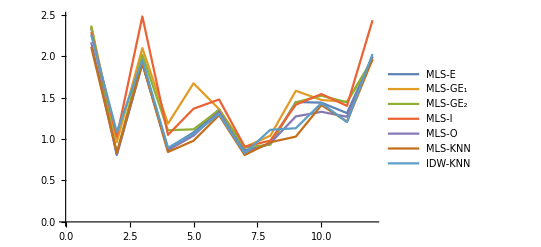

```mathematica
ListLinePlot[{MinMAEmethE,MinMAEmethG1E,MinMAEmethG2E,MinMAEmethI,MinMAEmethO,MinMAEmethKNNMLS,MinMAEmethKNNIDW},PlotLegends->{"MLS-E","MLS-GE_1","MLS-GE_2","MLS-I","MLS-O","MLS-KNN","IDW-KNN"}]
```

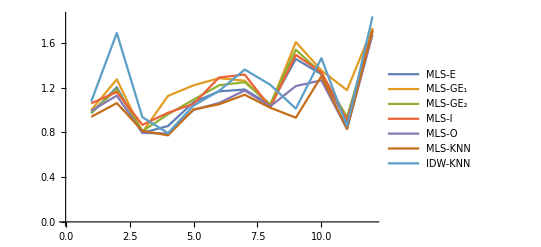

```mathematica
ListLinePlot[{MaxMAEmethE,MaxMAEmethG1E,MaxMAEmethG2E,MaxMAEmethI,MaxMAEmethO,MaxMAEmethKNNMLS,MaxMAEmethKNNIDW},PlotLegends->{"MLS-E","MLS-GE_1","MLS-GE_2","MLS-I","MLS-O","MLS-KNN","IDW-KNN"}]
```

```mathematica
TableForm[AllPointsMeanNumb=Table[Subscript[PointsMeanNumb, month][[i]],{month,1,totalMonth},{i,1,5}]];
```

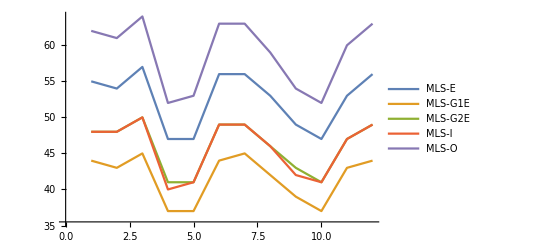

```mathematica
ListLinePlot[Transpose[AllPointsMeanNumb],PlotLegends->{"MLS-E","MLS-G1E","MLS-G2E","MLS-I","MLS-O"}]
```

```mathematica
MatrixForm[AlldimInOut=Table[{Subscript[dimIn, month],Subscript[dimOut, month]},{month,1,totalMonth}]];
```

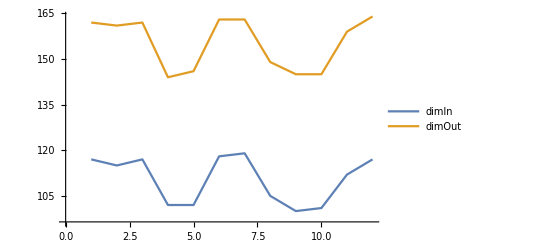

```mathematica
ListLinePlot[Transpose[AlldimInOut],PlotLegends->{"dimIn","dimOut"}]
```

```mathematica
MatrixForm[AllPointsN=Table[{Subscript[PointsMeanNumb, month][[1]],Subscript[PointsMeanNumb, month][[2]],Subscript[PointsMeanNumb, month][[3]],Subscript[PointsMeanNumb, month][[4]],Subscript[PointsMeanNumb, month][[5]],Subscript[kIndex, month],Subscript[kIndex, month]},{month,1,totalMonth}]]
```

(55 | 44 | 48 | 48 | 62 | 51 | 51
54 | 43 | 48 | 48 | 61 | 51 | 51
57 | 45 | 50 | 50 | 64 | 53 | 53
47 | 37 | 41 | 40 | 52 | 43 | 43
47 | 37 | 41 | 41 | 53 | 44 | 44
56 | 44 | 49 | 49 | 63 | 52 | 52
56 | 45 | 49 | 49 | 63 | 52 | 52
53 | 42 | 46 | 46 | 59 | 49 | 49
49 | 39 | 43 | 42 | 54 | 45 | 45
47 | 37 | 41 | 41 | 52 | 44 | 44
53 | 43 | 47 | 47 | 60 | 50 | 50
56 | 44 | 49 | 49 | 63 | 52 | 52)

```mathematica
Subscript[RMSDelMinTableAll, 1]*Log[AllPointsN[[1,All]]]
```

{13.9135,13.4606,13.5911,12.2285,11.628,10.7178,11.3093}

```mathematica
AllPoints=Table[{Subscript[PointsMeanNumb, month][[1]],Subscript[PointsMeanNumb, month][[2]],Subscript[PointsMeanNumb, month][[3]],Subscript[PointsMeanNumb, month][[4]],Subscript[PointsMeanNumb, month][[5]],Subscript[kIndex, month],Subscript[dimIn, month],Subscript[dimOut, month]},{month,1,totalMonth}];
```

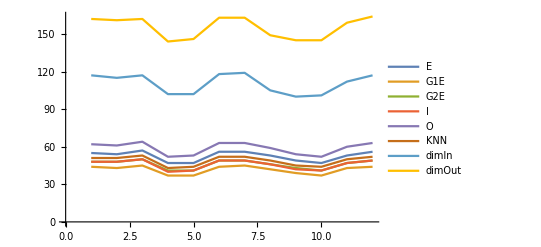

```mathematica
ListLinePlot[Transpose[AllPoints],PlotLegends->{"E","G1E","G2E","I","O","KNN","dimIn","dimOut"}]
```